```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\cheby\LPA\v2\phase\CP

```mathematica
alistT25=Flatten[Import["./T25/buffer/a.dat"]];
alist1T25=Rest[alistT25];
alistT26=Flatten[Import["./T26/buffer/a.dat"]];
alist1T26=Rest[alistT26];
alistT26p3=Flatten[Import["./T26p3/buffer/a.dat"]];
alist1T26p3=Rest[alistT26p3];
alistT26p4=Flatten[Import["./T26p4/buffer/a.dat"]];
alist1T26p4=Rest[alistT26p4];
alistT26p5=Flatten[Import["./T26p5/buffer/a.dat"]];
alist1T26p5=Rest[alistT26p5];
alistT27=Flatten[Import["./T27/buffer/a.dat"]];
alist1T27=Rest[alistT27];
alistT25p5=Flatten[Import["./T25p05/buffer/a.dat"]];
alist1T25p5=Rest[alistT25p5];
```

```mathematica
rhoend=250;
ρmin=0.;
ρmax=9000.;
sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/191}];
VallT25=Table[Evaluate[(test=SetPrecision[Sum[alist1T25[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[alistT25],52])],{ρ,0,rhoend,rhoend/191}];
VdataT25=Transpose[{sigma,VallT25-VallT25[[1]]+10^7}];
VallT26=Table[Evaluate[(test=SetPrecision[Sum[alist1T26[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[alistT26],52])],{ρ,0,rhoend,rhoend/191}];
VdataT26=Transpose[{sigma,VallT26-VallT26[[1]]+10^7}];
VallT26p3=Table[Evaluate[(test=SetPrecision[Sum[alist1T26p3[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[alistT26p3],52])],{ρ,0,rhoend,rhoend/191}];
VdataT26p3=Transpose[{sigma,VallT26p3-VallT26p3[[1]]+10^7}];
VallT26p4=Table[Evaluate[(test=SetPrecision[Sum[alist1T26p4[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[alistT26p4],52])],{ρ,0,rhoend,rhoend/191}];
VdataT26p4=Transpose[{sigma,VallT26p4-VallT26p4[[1]]+10^7}];
VallT26p5=Table[Evaluate[(test=SetPrecision[Sum[alist1T26p5[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[alistT26p5],52])],{ρ,0,rhoend,rhoend/191}];
VdataT26p5=Transpose[{sigma,VallT26p5-VallT26p5[[1]]+10^7}];
VallT25p5=Table[Evaluate[(test=SetPrecision[Sum[alist1T25p5[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[alistT25p5],52])],{ρ,0,rhoend,rhoend/191}];
VdataT25p5=Transpose[{sigma,VallT25p5-VallT25p5[[1]]+10^7}];
VallT27=Table[Evaluate[(test=SetPrecision[Sum[alist1T27[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[alistT27],52])],{ρ,0,rhoend,rhoend/191}];
VdataT27=Transpose[{sigma,VallT27-VallT27[[1]]+10^7}];
```

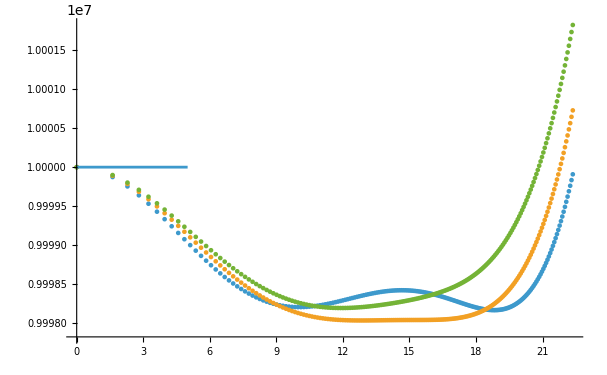

```mathematica
Show[ListPlot[{VdataT25,VdataT26p5(*,VdataT25p5*),VdataT27},PlotRange->All],ListLinePlot[{{0,10^7},{5,10^7}}]]
```